#### Lazy Linearity Attack

```mathematica
costLLA[lambda_,m_,g_] := 2^g/CDF[NormalDistribution[lambda, Sqrt[m]/2], 8];
Log[2,N[costLLA[150,1200, 10]]]
Log[2,N[costLLA[128,1000, 10]]]
Log[2,N[costLLA[150,1000, 10]]]
Log[2,N[costLLA[150,800, 10]]]
Log[2,N[costLLA[150,700, 10]]]
```

62.866

55.8234

72.691

87.3938

97.8779

#### Hamming’s razor

, , where .

```mathematica
ki[i_,m1_,h_] = If[i == 1, h*Log[2]/(Log[m1]+2), ki[1,m1,h]+(ki[i-1, m1, h]-1)*Log[ki[i-1, m1, h]]/(Log[m1]+2)];
```

```mathematica
N[ki[15, 200, 130]]
```

20.3161

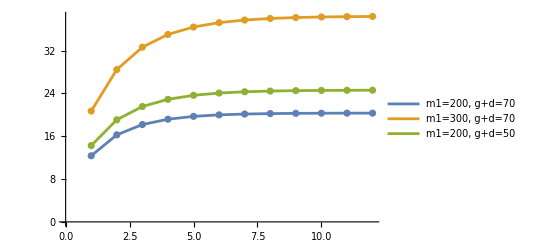

```mathematica
ListPlot[{Table[{i,ki[i,200,130]},{i,1,12}],Table[{i,ki[i,300,230]},{i,1,12}], Table[{i,ki[i,200,150]},{i,1,12}]},
Joined->True,Mesh->All, PlotLegends->{"m1=200, g+d="<>ToString[70], "m1=300, g+d="<>ToString[70],"m1=200, g+d="<>ToString[50]}]
```

When  are the same,  goes down as  goes up. When  are the same,  goes up as  goes up.

We want .

```mathematica
upperValue[m1_,m_,r_,lambda_]:=m1 - m1*(m/2+lambda-r)/(m-m1)
```

```mathematica
m1=200;m=1000;r=70;
h=m1-r;
N[ki[15, m1, h]]
N[upperValue[m1,m,r,150]]
```

20.3161

55.

```mathematica
m1=150;m=800;r=70;
h=m1-r;
N[ki[15, m1, h]]
N[upperValue[m1,m,r,150]]
```

11.6298

39.2308

```mathematica
m1=30;m=200;r=14;
h=m1-r;
N[ki[15, m1, h]]
N[upperValue[m1,m,r,50]]
```

2.23795

6.

Let us compute other parameters.

```mathematica
n[m_,lambda_]:=m/2+lambda;
{n[1000, 150], n[1200, 150]}
```

{650,750}

```mathematica
w[m_, m1_,g_,lambda_]:=n[m,lambda]-g-(m-m1);
{w[1000, 400, 10,150],w[1200, 450, 10,150],w[1500, 550, 10,150]}
```

{40,-10,90}

```mathematica
m = 1200;
m2=750;
n[m,150]
w[m,m-m2,10,150]
```

750

-10

#### Radical Attack with row deletion

The probability that randomly selecting  rows which turn out to all be redundant rows is

```mathematica
probRed[m_,m2_,k_]:=If[k==1, m2/m, probRed[m,m2,k-1]*(m2-k+1)/(m-k+1)]
```

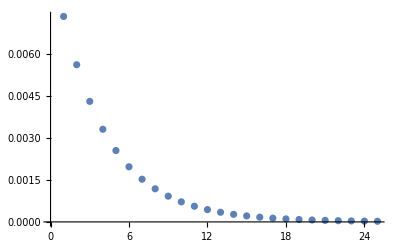

```mathematica
ListPlot[Table[{i,N[probRed[1000,750+i,16+i]]},{i,1,25}]]
```

```mathematica
m=800;
m2=650;
n[m,150]
w[m,m-m2,10,150]
N[probRed[m,m2,6-w[m,m-m2,10,150]]]
Log[2,N[probRed[m,m2,6-w[m,m-m2,10,150]]]]
```

550

-110

3.99668×10^-12

-37.8643

```mathematica
m=1000;
m2=800;
n[m,150]
w[m,m-m2,10,150]
N[probRed[m,m2,6-w[m,m-m2,10,150]]]
Log[2,N[probRed[m,m2,6-w[m,m-m2,10,150]]]]
```

650

-160

1.62542×10^-18

-59.0939

```mathematica
m=700;
m2=600;
n[m,150]
w[m,m-m2,10,150]
N[probRed[m,m2,6-w[m,m-m2,10,150]]]
Log[2,N[probRed[m,m2,6-w[m,m-m2,10,150]]]]
```

500

-110

2.81434×10^-9

-28.4046